# Cylindrical Magnet Multipole Field

## Main Functions

```mathematica
r[ϕ,θ] (*position unit vector of observation*)
x[R,α] (*position vector of source *)
k[R,L]:=√(R^2+(L/2)^2) (*length of the source vector*)
h[R,α,θ] (* dot product of observation vector and ssource vector *)
```

```mathematica
(* The field is with out m/(4π) *)
```

```mathematica
Q[a,L,l,θ] (* the surface integral of external field*)
ExtH[n,a,L,R,θ] (* external H-field in spherical coordinate *)
ExtHRec[n,a,L,X,Z] (* external H-field in Rectangle coordinate *)
DrawRec[a,L] (* Rectangle Draw *)
GraphExtH[n,a,L,Color] (* Graph of External H-field of order n *)
SumGraphExtH[m,a,L,Color] (* Graph of the sum of external H-field form order 0 to m *)
```

```mathematica
S[a,L,l,θ] (* the surface integral of Internal field*)
IntH[n,a,L,R,θ] (* internal H-field in spherical coordinate *)
IntHRec[n,a,L,X,Z] (* Internal H-field in Rectangle coordinate *)
GraphIntH[n,a,L,Color] (* Graph of Internal H-field of order n *)
SumGraphIntH[m,a,L,Color] (* Graph of the sum of Internal H-field form order 0 to m *)
```

```mathematica
GraphIntB[n,a,L,ColorH,ColorB] (* Graph of Internal B-field of order n *)
SumGraphIntH[m,a,L,ColorH, ColorB] (* Graph of the sum of Internal B-field form order 0 to m *)
```

## Exterior Field Calculation

```mathematica
(* magnetic scalr potential *)
Φm=1/(4π)∫(μ.n)/Norm[r-x] ⅆa
```

```mathematica
(* Magnetization *)
μ=M{0,0,1};
(* surface normal *)
n1={0,0,1};
n2={Cos[α],Sin[α],0};
n3={0,0,-1};
(* μ.n *)
μ.n1
μ.n2
μ.n3
```

M

0

-M

```mathematica
r[ϕ_,θ_]:={Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]};
x[R_,α_]:=1/(√(R^2+(L/2)^2)){R Cos[α],R Sin[α],L/2};
k[R_,L_]:=√(R^2+(L/2)^2);
h[R_,α_,θ_]:=r[0,θ].x[R,α]//Simplify
h[R,α,θ]
```

(L Cos[θ]+2 R Cos[α] Sin[θ])/(√(L^2+4 R^2))

```mathematica
(* surface integral *)
Q[a_,L_,l_,θ_]:=Simplify[1/(π a^2 L)Integrate[Evaluate[Cancel[(k[R,L])^l LegendreP[l,h[R,α,θ]]R]],{α,0,2π},{R,0,a}],{a>0,L>0}]
```

```mathematica
genExtH[n_,a_,L_,r_,θ_]:={ (2n+2)/r^(2n+3)Q[a,L,2n+1,θ],-1/r^(2n+3)Evaluate[D[Q[a,L,2n+1,β],β]/.β->θ]}//Simplify
```

```mathematica
StoreExtH=Table[genExtH[n,a,L,R,θ],{n,0,5}]
```

{{Cos[θ]/R^3,Sin[θ]/(2 R^3)},{-((3 a^2-L^2) (3 Cos[θ]+5 Cos[3 θ]))/(16 R^5),-(3 (3 a^2-L^2) (Sin[θ]+5 Sin[3 θ]))/(64 R^5)},{(3 (10 a^4-10 a^2 L^2+L^4) (30 Cos[θ]+35 Cos[3 θ]+63 Cos[5 θ]))/(2048 R^7),(15 (10 a^4-10 a^2 L^2+L^4) (2 Sin[θ]+7 (Sin[3 θ]+3 Sin[5 θ])))/(4096 R^7)},{-((35 a^6-70 a^4 L^2+21 a^2 L^4-L^6) (175 Cos[θ]+189 Cos[3 θ]+231 Cos[5 θ]+429 Cos[7 θ]))/(16384 R^9),-(7 (35 a^6-70 a^4 L^2+21 a^2 L^4-L^6) (25 Sin[θ]+81 Sin[3 θ]+165 Sin[5 θ]+429 Sin[7 θ]))/(131072 R^9)},{1/(8388608 R^11)5 (126 a^8-420 a^6 L^2+252 a^4 L^4-36 a^2 L^6+L^8) (4410 Cos[θ]+11 (420 Cos[3 θ]+13 (36 Cos[5 θ]+45 Cos[7 θ]+85 Cos[9 θ]))),1/(16777216 R^11)45 (126 a^8-420 a^6 L^2+252 a^4 L^4-36 a^2 L^6+L^8) (98 Sin[θ]+11 (28 Sin[3 θ]+52 Sin[5 θ]+91 Sin[7 θ]+221 Sin[9 θ]))},{-1/(134217728 R^13)3 (462 a^10-2310 a^8 L^2+2310 a^6 L^4-660 a^4 L^6+55 a^2 L^8-L^10) (29106 Cos[θ]+13 (2310 Cos[3 θ]+2475 Cos[5 θ]+2805 Cos[7 θ]+3553 Cos[9 θ]+6783 Cos[11 θ])),-1/(536870912 R^13)33 (462 a^10-2310 a^8 L^2+2310 a^6 L^4-660 a^4 L^6+55 a^2 L^8-L^10) (882 Sin[θ]+13 (210 Sin[3 θ]+375 Sin[5 θ]+595 Sin[7 θ]+969 Sin[9 θ]+2261 Sin[11 θ]))}}

```mathematica
ExtH[n_,b_,M_,P_,β_]:=StoreExtH[[n+1]]/.{a->b,L->M,R->P,θ->β}
ExtH[0,j,n,o,t]
```

{Cos[t]/o^3,Sin[t]/(2 o^3)}

## Exterior Field Display

```mathematica
Cos[θ]=Z/(√(X^2+Z^2))
Sin[θ]=X/(√(X^2+Z^2))
```

```mathematica
Clear[X,Z]
```

```mathematica
(* convert to Cartesian coordinate *)
ConvtExtH2Rec[n_]:=FullSimplify[ExtH[n,a,L,√(X^2+Z^2),ArcSin[X/(√(X^2+Z^2))]][[1]]{X/(√(X^2+Z^2)),Z/(√(X^2+Z^2))}+ExtH[n,a,L,√(X^2+Z^2),ArcSin[X/(√(X^2+Z^2))]][[2]]{Z/(√(X^2+Z^2)),-X/(√(X^2+Z^2))},{Z>0,X>0,X^2+Z^2>0}]
```

```mathematica
StoreExtHRec=Table[ConvtExtH2Rec[n],{n,0,5}]
```

{{(3 X Z)/(2 (X^2+Z^2)^(5/2)),(-X^2+2 Z^2)/(2 (X^2+Z^2)^(5/2))},{(5 (3 a^2-L^2) X Z (3 X^2-4 Z^2))/(16 (X^2+Z^2)^(9/2)),-((3 a^2-L^2) (3 X^4-24 X^2 Z^2+8 Z^4))/(16 (X^2+Z^2)^(9/2))},{(21 (10 a^4-10 a^2 L^2+L^4) X Z (5 X^4-20 X^2 Z^2+8 Z^4))/(256 (X^2+Z^2)^(13/2)),-(3 (10 a^4-10 a^2 L^2+L^4) (5 X^6-90 X^4 Z^2+120 X^2 Z^4-16 Z^6))/(256 (X^2+Z^2)^(13/2))},{(9 (35 a^6-70 a^4 L^2+21 a^2 L^4-L^6) X Z (35 X^6-280 X^4 Z^2+336 X^2 Z^4-64 Z^6))/(2048 (X^2+Z^2)^(17/2)),-((35 a^6-70 a^4 L^2+21 a^2 L^4-L^6) (35 X^8-1120 X^6 Z^2+3360 X^4 Z^4-1792 X^2 Z^6+128 Z^8))/(2048 (X^2+Z^2)^(17/2))},{1/(65536 (X^2+Z^2)^(21/2))55 (126 a^8-420 a^6 L^2+252 a^4 L^4-36 a^2 L^6+L^8) X Z (63 X^8-840 X^6 Z^2+2016 X^4 Z^4-1152 X^2 Z^6+128 Z^8),-1/(65536 (X^2+Z^2)^(21/2))5 (126 a^8-420 a^6 L^2+252 a^4 L^4-36 a^2 L^6+L^8) (63 X^10-3150 X^8 Z^2+16800 X^6 Z^4-20160 X^4 Z^6+5760 X^2 Z^8-256 Z^10)},{1/(524288 (X^2+Z^2)^(25/2))39 (462 a^10-2310 a^8 L^2+2310 a^6 L^4-660 a^4 L^6+55 a^2 L^8-L^10) X Z (231 X^10-4620 X^8 Z^2+18480 X^6 Z^4-21120 X^4 Z^6+7040 X^2 Z^8-512 Z^10),-1/(524288 (X^2+Z^2)^(25/2))3 (462 a^10-2310 a^8 L^2+2310 a^6 L^4-660 a^4 L^6+55 a^2 L^8-L^10) (231 X^12-16632 X^10 Z^2+138600 X^8 Z^4-295680 X^6 Z^6+190080 X^4 Z^8-33792 X^2 Z^10+1024 Z^12)}}

```mathematica
ExtHRec[n_,p_,q_,s_,t_]:=StoreExtHRec[[n+1]]/.{a->p,L->q,X->s,Z->t}
```

```mathematica
DrawRec[a_,L_]:=Graphics[{EdgeForm[Thin],Transparent,Rectangle[{-a,-L/2},{a,L/2}]}]
GraphExtH[n_,a_,L_,Color_]:=Show[StreamPlot[ExtHRec[n,a,L,X,Z],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->Color,RegionFunction->Function[{X,Z},X^2+Z^2>a^2+(L/2)^2]],DrawRec[a,L]]
SumGraphExtH[m_,a_,L_,Color_]:=Show[StreamPlot[Sum[ExtHRec[n,a,L,X,Z],{n,0,m}],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->Color,RegionFunction->Function[{X,Z},X^2+Z^2>a^2+(L/2)^2]],DrawRec[a,L]]
```

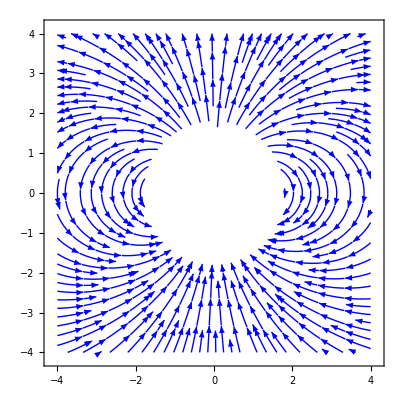

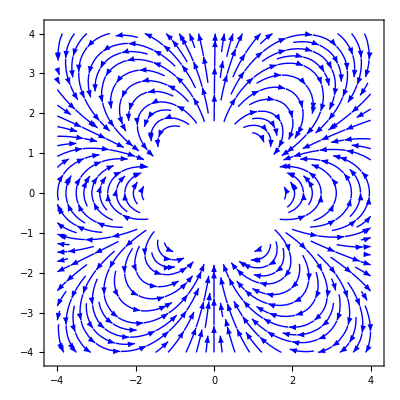

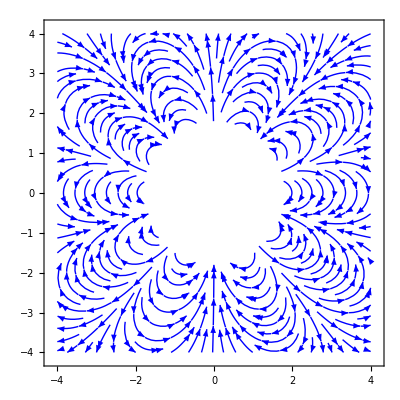

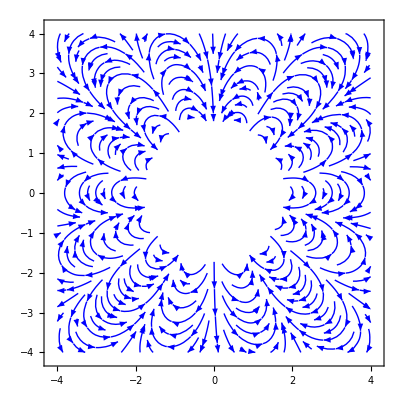

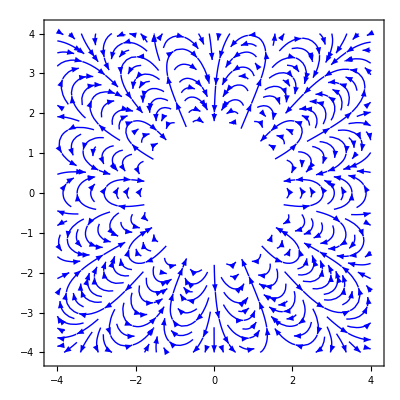

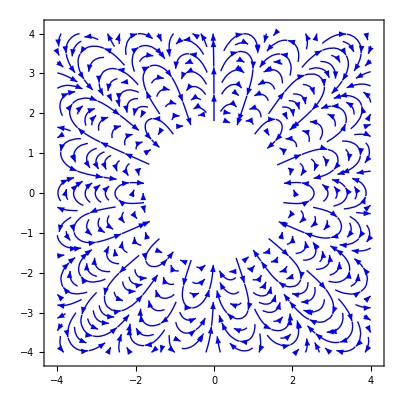

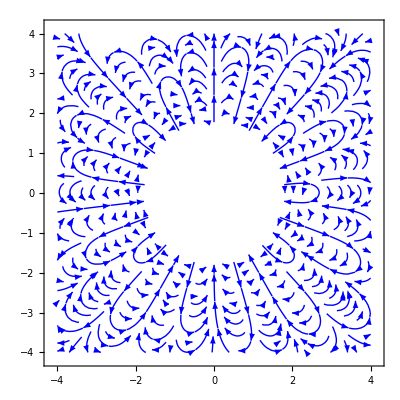

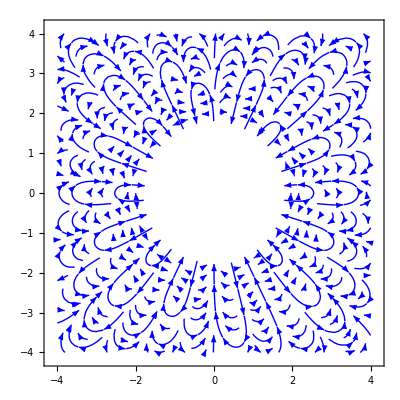

```mathematica
GrExtH0=GraphExtH[0,1,3,Blue]
GrExtH1=GraphExtH[1,1,3,Blue]
GrExtH2=GraphExtH[2,1,3,Blue]
GrExtH3=GraphExtH[3,1,3,Blue]
GrExtH4=GraphExtH[4,1,3,Blue]
GrExtH5=GraphExtH[5,1,3,Blue]
GrExtH6=GraphExtH[6,1,3,Blue]
GrExtH7=GraphExtH[7,1,3,Blue]
```

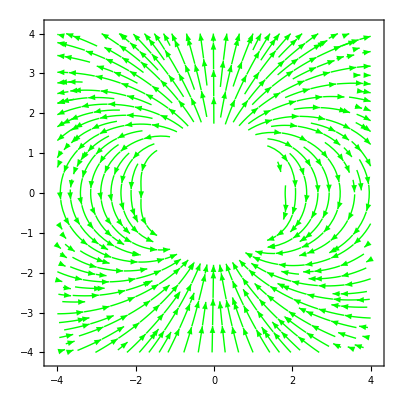

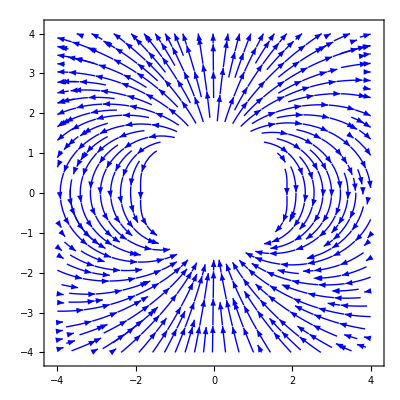

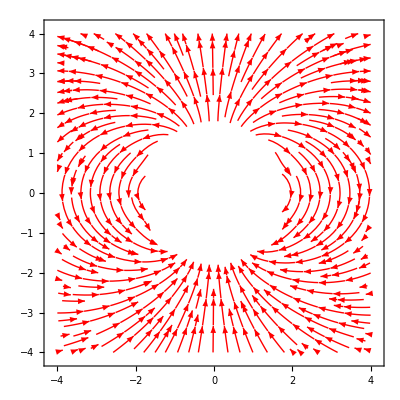

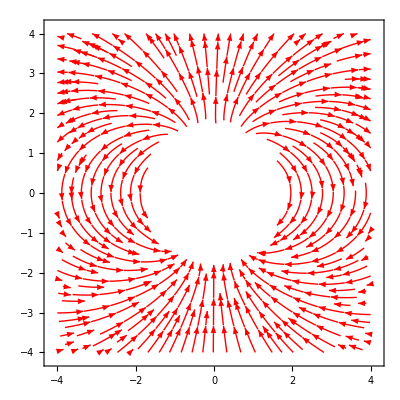

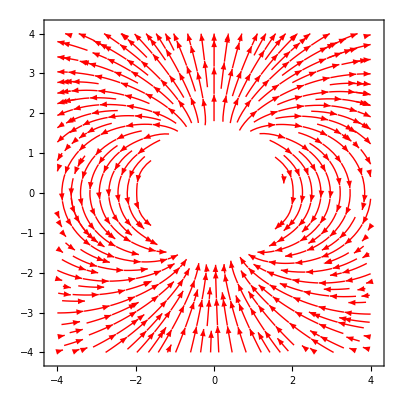

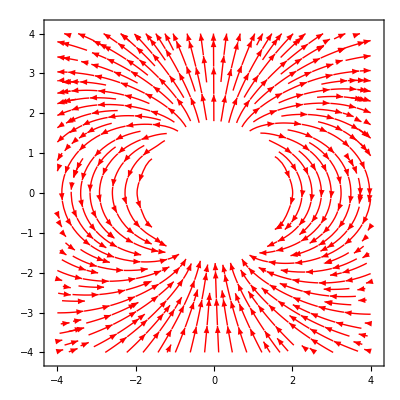

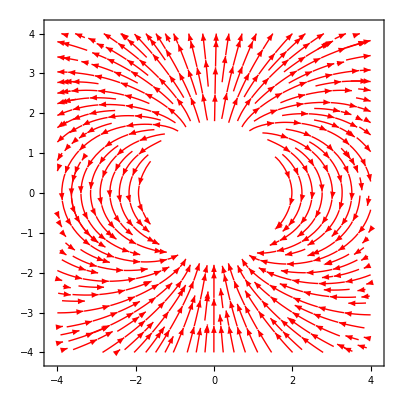

```mathematica
SG1=SumGraphExtH[1,1,3,RGBColor[0,1,0]]
SG2=SumGraphExtH[2,1,3,RGBColor[0,0,1]]
SG3=SumGraphExtH[3,1,3,RGBColor[1,0,0]]
SG4=SumGraphExtH[4,1,3,RGBColor[1,0,0]]
SG5=SumGraphExtH[5,1,3,RGBColor[1,0,0]]
SG6=SumGraphExtH[6,1,3,RGBColor[1,0,0]]
SG7=SumGraphExtH[7,1,3,RGBColor[1,0,0]]
```

## Interior Field Calculation

```mathematica
(* surface integral *)
ExpS[l_,L_,α_,θ_,R_]:=Expand[(1/k[R,L])^(l+1)LegendreP[l,h[R,α,θ]]R]
StoreExpS=Table[ExpS[2n+1,L,α,θ,R],{n,0,5}];
```

```mathematica
InDefinedS[a_,L_,l_,θ_,α_,R_]:=1/(π a^2 L)Integrate[StoreExpS[[(l+1)/2]],α,R]
```

```mathematica
StoreInDSαR=Table[InDefinedS[a,L,2n+1,θ,α,R],{n,0,5}];
```

```mathematica
StoreInDSR=(StoreInDSαR/.{α->2π})-(StoreInDSαR/.{α->0});
StoreS=(StoreInDSR/.{R->a})-(StoreInDSR/.{R->0})//Simplify
```

{(2 (1/(√(L^2))-1/(√(4 a^2+L^2))) Cos[θ])/a^2,(4 Cos[θ] (-1+5 Cos[2 θ]))/((4 a^2+L^2)^(5/2)),((-3 a^2+L^2) (30 Cos[θ]+35 Cos[3 θ]+63 Cos[5 θ]))/(2 (4 a^2+L^2)^(9/2)),((10 a^4-10 a^2 L^2+L^4) (175 Cos[θ]+189 Cos[3 θ]+231 Cos[5 θ]+429 Cos[7 θ]))/(4 (4 a^2+L^2)^(13/2)),1/(32 (4 a^2+L^2)^(17/2))(-35 a^6+70 a^4 L^2-21 a^2 L^4+L^6) (4410 Cos[θ]+11 (420 Cos[3 θ]+13 (36 Cos[5 θ]+45 Cos[7 θ]+85 Cos[9 θ]))),1/(64 (4 a^2+L^2)^(21/2))(126 a^8-420 a^6 L^2+252 a^4 L^4-36 a^2 L^6+L^8) (29106 Cos[θ]+13 (2310 Cos[3 θ]+2475 Cos[5 θ]+2805 Cos[7 θ]+3553 Cos[9 θ]+6783 Cos[11 θ]))}

```mathematica
S[p_,q_,l_,ϕ_]:=StoreS[[(l+1)/2]]/.{a->p,L->q,θ->ϕ}
genIntH[n_,a_,L_,R_,θ_]:=-{R^(2n)(2n+1)S[a,L,2n+1,θ],R^(2n)D[S[a,L,2n+1,θ],θ]}
```

```mathematica
StoregenIntH=Table[genIntH[n,a,L,R,θ],{n,0,5}];
```

```mathematica
IntH[n_,p_,q_,g_,ϕ_] :=StoregenIntH[[n+1]]/.{a->p,L->q,R->g,θ->ϕ}
```

```mathematica
Table[IntH[n,a,L,R,θ],{n,0,5}]
```

{{-(2 (1/(√(L^2))-1/(√(4 a^2+L^2))) Cos[θ])/a^2,(2 (1/(√(L^2))-1/(√(4 a^2+L^2))) Sin[θ])/a^2},{-(12 R^2 Cos[θ] (-1+5 Cos[2 θ]))/((4 a^2+L^2)^(5/2)),-R^2 (-(4 (-1+5 Cos[2 θ]) Sin[θ])/((4 a^2+L^2)^(5/2))-(40 Cos[θ] Sin[2 θ])/((4 a^2+L^2)^(5/2)))},{-(5 (-3 a^2+L^2) R^4 (30 Cos[θ]+35 Cos[3 θ]+63 Cos[5 θ]))/(2 (4 a^2+L^2)^(9/2)),-((-3 a^2+L^2) R^4 (-30 Sin[θ]-105 Sin[3 θ]-315 Sin[5 θ]))/(2 (4 a^2+L^2)^(9/2))},{-(7 (10 a^4-10 a^2 L^2+L^4) R^6 (175 Cos[θ]+189 Cos[3 θ]+231 Cos[5 θ]+429 Cos[7 θ]))/(4 (4 a^2+L^2)^(13/2)),-((10 a^4-10 a^2 L^2+L^4) R^6 (-175 Sin[θ]-567 Sin[3 θ]-1155 Sin[5 θ]-3003 Sin[7 θ]))/(4 (4 a^2+L^2)^(13/2))},{-1/(32 (4 a^2+L^2)^(17/2))9 (-35 a^6+70 a^4 L^2-21 a^2 L^4+L^6) R^8 (4410 Cos[θ]+11 (420 Cos[3 θ]+13 (36 Cos[5 θ]+45 Cos[7 θ]+85 Cos[9 θ]))),-1/(32 (4 a^2+L^2)^(17/2))(-35 a^6+70 a^4 L^2-21 a^2 L^4+L^6) R^8 (-4410 Sin[θ]+11 (-1260 Sin[3 θ]+13 (-180 Sin[5 θ]-315 Sin[7 θ]-765 Sin[9 θ])))},{-1/(64 (4 a^2+L^2)^(21/2))11 (126 a^8-420 a^6 L^2+252 a^4 L^4-36 a^2 L^6+L^8) R^10 (29106 Cos[θ]+13 (2310 Cos[3 θ]+2475 Cos[5 θ]+2805 Cos[7 θ]+3553 Cos[9 θ]+6783 Cos[11 θ])),-1/(64 (4 a^2+L^2)^(21/2))(126 a^8-420 a^6 L^2+252 a^4 L^4-36 a^2 L^6+L^8) R^10 (-29106 Sin[θ]+13 (-6930 Sin[3 θ]-12375 Sin[5 θ]-19635 Sin[7 θ]-31977 Sin[9 θ]-74613 Sin[11 θ]))}}

```mathematica
IntH[2,a,L,R,θ]//Simplify
```

{-(5 (-3 a^2+L^2) R^4 (30 Cos[θ]+35 Cos[3 θ]+63 Cos[5 θ]))/(2 (4 a^2+L^2)^(9/2)),-(15 (3 a^2-L^2) R^4 (2 Sin[θ]+7 (Sin[3 θ]+3 Sin[5 θ])))/(2 (4 a^2+L^2)^(9/2))}

## Interior Field Display

```mathematica
Cos[θ]=Z/(√(X^2+Z^2))
Sin[θ]=X/(√(X^2+Z^2))
```

```mathematica
(* convert to Cartesian coordinate *)
ConvtIntH2Rec[n_]:=FullSimplify[IntH[n,a,L,√(X^2+Z^2),ArcSin[X/(√(X^2+Z^2))]][[1]]{X/(√(X^2+Z^2)),Z/(√(X^2+Z^2))}+IntH[n,a,L,√(X^2+Z^2),ArcSin[X/(√(X^2+Z^2))]][[2]]{Z/(√(X^2+Z^2)),-X/(√(X^2+Z^2))},{Z>0,X>0,X^2+Z^2>0}]
```

```mathematica
StoreIntHRec=Table[ConvtIntH2Rec[n],{n,0,5}];
```

```mathematica
IntHRec[n_,p_,q_,s_,t_]:=StoreIntHRec[[n+1]]/.{a->p,L->q,X->s,Z->t}
```

```mathematica
GraphIntH[n_,a_,L_,Color_]:=Show[StreamPlot[IntHRec[n,a,L,X,Z],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->Color,RegionFunction->Function[{X,Z},X^2+Z^2≤ (L/2)^2]],DrawRec[a,L]]
SumGraphIntH[m_,a_,L_,Color_]:=Show[StreamPlot[Sum[IntHRec[n,a,L,X,Z],{n,0,m}],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->Color,RegionFunction->Function[{X,Z},X^2+Z^2≤ (L/2)^2]],DrawRec[a,L]]
```

## Magnetic Flux Density - B

```mathematica
(* inside the material, the magnetci field is sum of H-field and M *)
μRec[a_,L_]:=1/(π a^2 L){0,1}
```

```mathematica
GraphIntB[n_,a_,L_,ColorH_,ColorB_]:=Show[
StreamPlot[IntHRec[n,a,L,X,Z]+μRec[a,L],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->ColorB,RegionFunction->Function[{X,Z},(Abs[X]<a && Abs[Z]<L/2&&X^2+Z^2≤ (L/2)^2)]],
StreamPlot[IntHRec[n,a,L,X,Z],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->ColorH,RegionFunction->Function[{X,Z},((Abs[X]>a ||Abs[Z]>L/2)&&X^2+Z^2≤ (L/2)^2)]],
DrawRec[a,L]]
SumGraphIntB[m_,a_,L_,ColorH_,ColorB_]:=Show[
StreamPlot[Sum[IntHRec[n,a,L,X,Z],{n,0,m}]+μRec[a,L],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->ColorB,RegionFunction->Function[{X,Z},(Abs[X]<a && Abs[Z]<L/2&&X^2+Z^2≤ (L/2)^2)]],
StreamPlot[Sum[IntHRec[n,a,L,X,Z],{n,0,m}],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->ColorH,RegionFunction->Function[{X,Z},((Abs[X]>a ||Abs[Z]>L/2)&&X^2+Z^2≤ (L/2)^2)]],
DrawRec[a,L]]
```

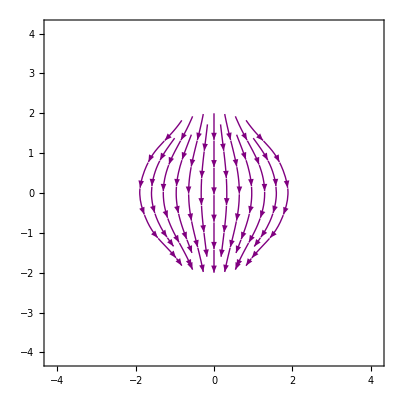

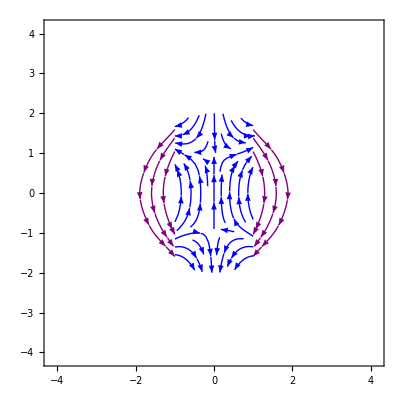

```mathematica
SumGraphIntH[3,1,4,Purple]
SumGraphIntB[3,1,4,Purple,Blue]
```

## Total field Display

```mathematica
GraphB[n_,a_,L_]:=Show[
GraphExtH[n,a,L,Blue],
GraphIntB[n,a,L,Purple,Red]]
SumGraphB[m_,a_,L_]:=Show[
SumGraphExtH[m,a,L,Blue],
SumGraphIntB[m,a,L,Purple,Red]]
```

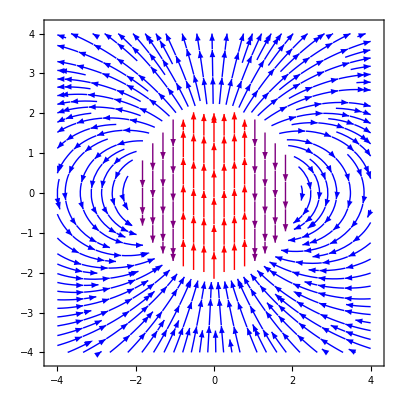

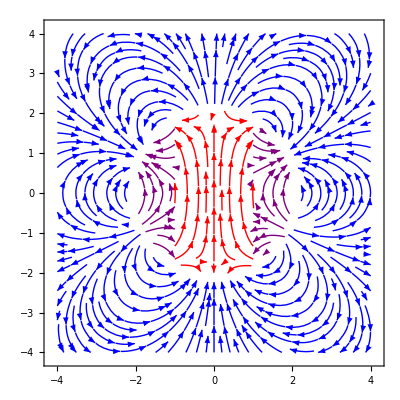

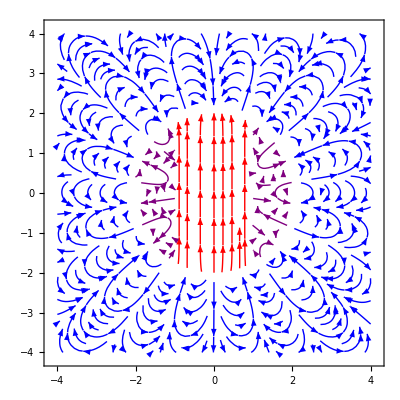

```mathematica
GraphB[0,1,4]
GraphB[1,1,4]
GraphB[5,1,4]
```

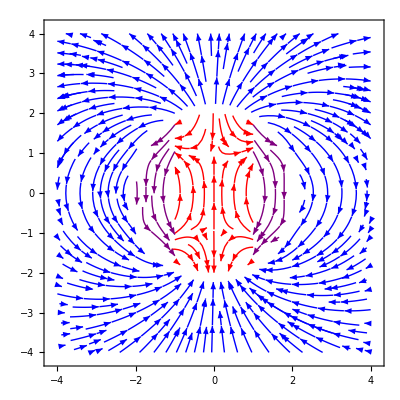

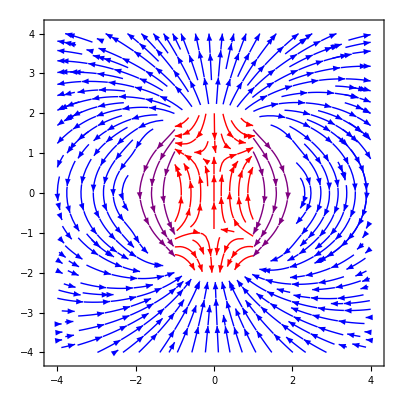

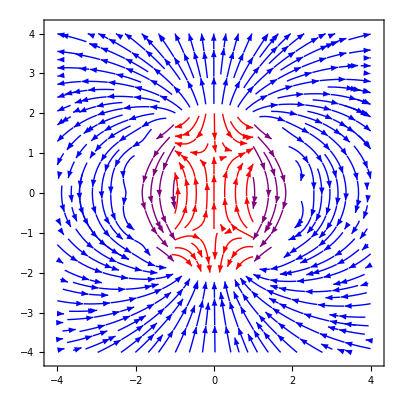

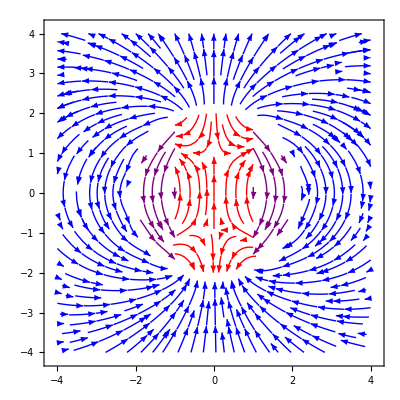

```mathematica
SumGraphB[2,1,4]
SumGraphB[3,1,4]
SumGraphB[4,1,4]
SumGraphB[5,1,4]
```

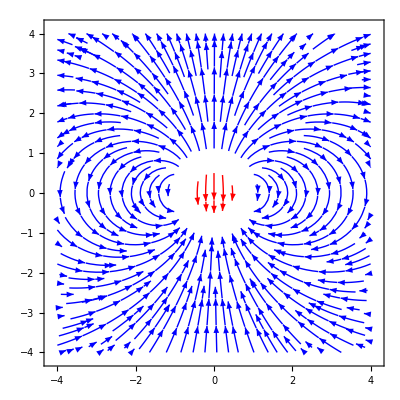

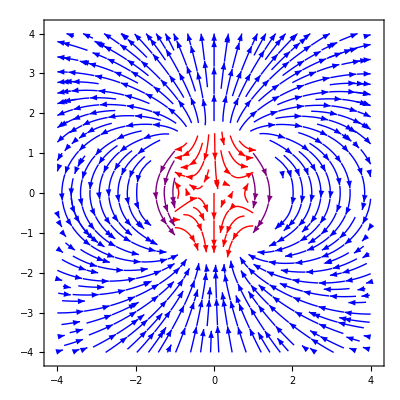

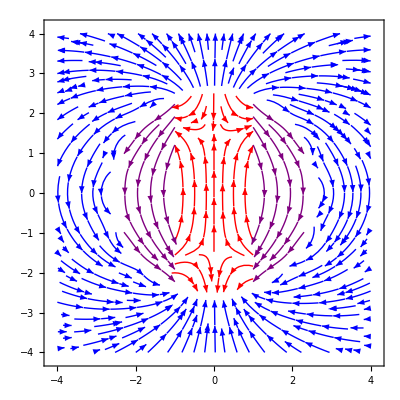

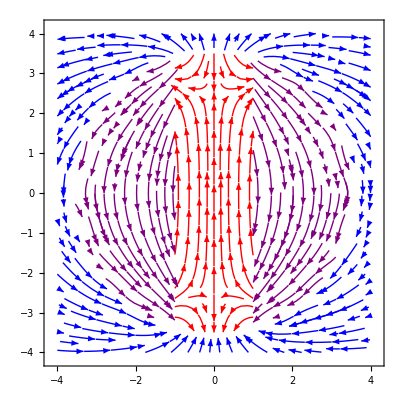

```mathematica
(* dimension *)
SumGraphB[5,1,1]
SumGraphB[5,1,3]
SumGraphB[5,1,5]
SumGraphB[5,1,7]
```

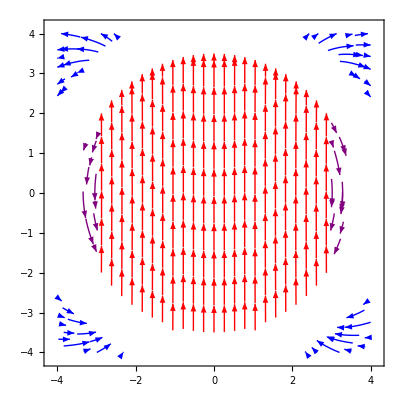

```mathematica
SumGraphB[5,3,7]
```

## Sand Box

```mathematica
GraphExtHK[n_,a_,L_,Color_]:=Show[StreamPlot[ExtHRec[n,a,L,X,Z],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->Color,RegionFunction->Function[{X,Z},X^2+Z^2>0]],DrawRec[a,L]]
SumGraphExtHK[m_,a_,L_,Color_]:=Show[StreamPlot[Sum[ExtHRec[n,a,L,X,Z],{n,0,m}],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->Color,RegionFunction->Function[{X,Z},X^2+Z^2>0]],DrawRec[a,L]]
```

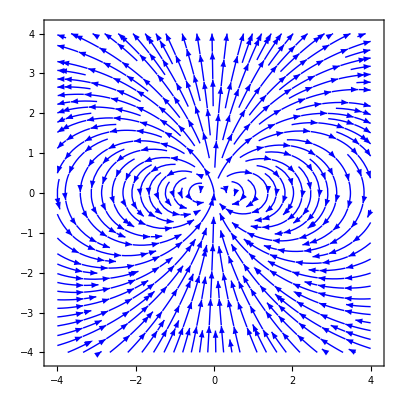

```mathematica
GraphExtHK[0,2,1,Blue]
```

```mathematica
GraphIntBK[n_,a_,L_,ColorH_,ColorB_]:=Show[
StreamPlot[IntHRec[n,a,L,X,Z]+μRec[a,L],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->ColorB,RegionFunction->Function[{X,Z},(Abs[X]<a && Abs[Z]<L/2&&X^2+Z^2≤ (L/2)^2)]],
StreamPlot[IntHRec[n,a,L,X,Z],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->ColorH,RegionFunction->Function[{X,Z},((Abs[X]>a ||Abs[Z]>L/2)&&X^2+Z^2≤ (L/2)^2)]],
DrawRec[a,L]]
SumGraphIntBK[m_,a_,L_,ColorH_,ColorB_]:=Show[
StreamPlot[Sum[IntHRec[n,a,L,X,Z],{n,0,m}]+μRec[a,L],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->ColorB,RegionFunction->Function[{X,Z},(Abs[X]<a && Abs[Z]<L/2&&X^2+Z^2≤ (L/2)^2)]],
StreamPlot[Sum[IntHRec[n,a,L,X,Z],{n,0,m}],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->ColorH,RegionFunction->Function[{X,Z},((Abs[X]>a ||Abs[Z]>L/2)&&X^2+Z^2≤ (L/2)^2)]],
DrawRec[a,L]]
```

```mathematica
AverageH[n_,a_,L_,Color_]:=Show[
StreamPlot[(IntHRec[n,a,L,X,Z]+ExtHRec[n,a,L,X,Z])1/2,{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->Color,RegionFunction->Function[{X,Z},((L/2)^2≤ X^2+Z^2≤a^2+ (L/2)^2)]],
DrawRec[a,L]]
SumAverageH[m_,a_,L_,Color_]:=Show[
StreamPlot[Sum[(IntHRec[n,a,L,X,Z]+ExtHRec[n,a,L,X,Z])1/2,{n,0,m}],{X,-4,4},{Z,-4,4},StreamPoints->Fine,StreamStyle->Color,RegionFunction->Function[{X,Z},((L/2)^2≤ X^2+Z^2≤a^2+ (L/2)^2)]],
DrawRec[a,L]]
```

```mathematica
FieldBK[n_,a_,L_]:=Show[
GraphExtHK[n,a,L,Blue],
AverageH[n,a,L,Pink],
GraphIntBK[n,a,L,Purple,Red]
]
SumFieldBK[n_,a_,L_]:=Show[
SumGraphExtHK[n,a,L,Blue],
AverageH[n,a,L,Pink],
SumGraphIntBK[n,a,L,Purple,Red]
]
```

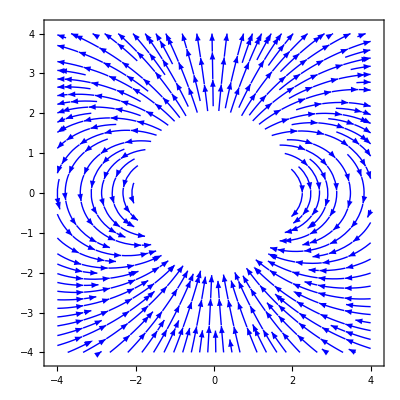

```mathematica
GraphExtH[0,2,1,Blue]
```

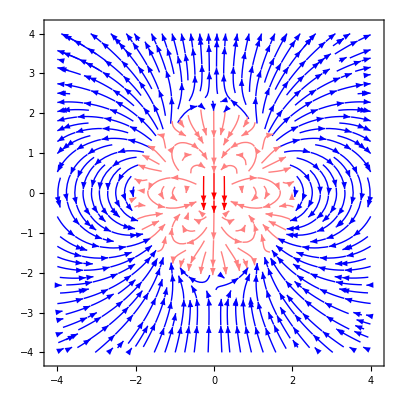

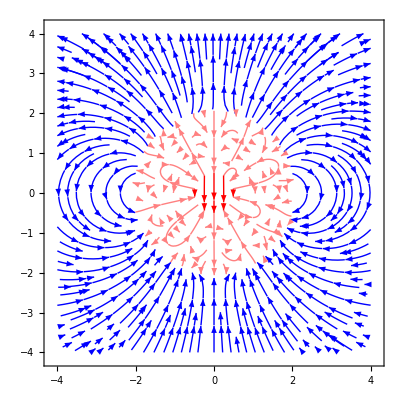

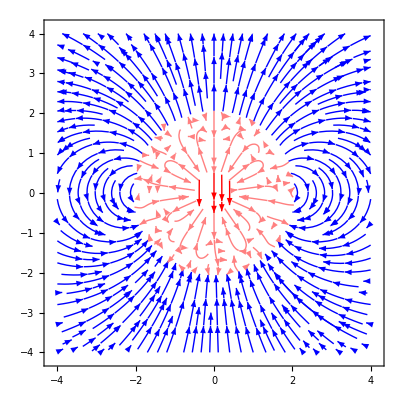

```mathematica
SumFieldBK[1,2,1]
SumFieldBK[3,2,1]
SumFieldBK[5,2,1]
```